```mathematica
"pnPlot";
```

```mathematica
ClearAll[Evaluate[Context[]<>"*"]];
```

```mathematica
SetDirectory@NotebookDirectory[];
AutoCollapse[]:=(If[$FrontEnd=!=$Failed,SelectionMove[EvaluationNotebook[],All,GeneratedCell];
FrontEndTokenExecute["SelectionCloseUnselectedCells"]]);
HideText[x_]:=(Print[x];AutoCollapse[]);
HideText["Basic setup"]
```

Basic setup

```mathematica
<<MaTeX`
(*ConfigureMaTeX["pdfLaTeX"->"C:\\texlive\\2016\\bin\\win32\\xelatex.exe"];*)
(*ConfigureMaTeX["pdfLaTeX"->"C:\\texlive\\2016\\bin\\win32\\pdflatex.exe"];*)
SetOptions[MaTeX,"Preamble"->{"\\usepackage{physics,nicefrac,esint,siunitx,bm}"}(*,"Magnification"->1.2*)];
MyTeX[x_]:=HideText[MaTeX[x]];
HideText["MaTeX Loaded"]
```

MaTeX Loaded

```mathematica
(*<<ErrorBarPlots`*)
```

```mathematica
omarker=Graphics[{Thickness[.2],Circle[]}];
colors=(("DefaultPlotStyle"/.(Method/.Charting`ResolvePlotTheme["Scientific",ListPlot]))/.Directive[x_,__]:>x);
HideText["omarker & colors"]
```

omarker & colors

```mathematica
tempRhoRaw=Import["data.xlsx"]⟦1⟧⟦3;;24,{6,14}⟧;
HideText["tempRhoRaw; temp in Celsius, rho in Ohm.cm"]
```

tempRhoRaw; temp in Celsius, rho in Ohm.cm

```mathematica
e=UnitConvert[Quantity["ElementaryCharge"],"Coulombs"]//QuantityMagnitude;
HideText@"def charge e"
```

def charge e

```mathematica
μp[tempK_]:=2.5*10^8*tempK^-2.3;
b[tempK_]:=16 tempK^(-.3);
```

```mathematica
na=1/(3474.5373804221495*e*μp[300])
```

3.57958×10^12

```mathematica
tempRhoPartial=Select[#⟦1⟧>70&]@tempRhoRaw;
```

```mathematica
logP={1000./(#1+273.15),
Log[(1/(#2*e*μp[#1+273.15])+b[#1+273.15]na)
1/(b[#1+273.15]+1)]}&@@@tempRhoPartial;
```

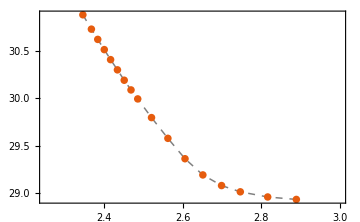

logPplot.pdf

```mathematica
logPplot=Show[ListLinePlot[logP,
PlotTheme->"Scientific",
(*PlotMarkers->{omarker,.012},*)
PlotStyle->{Dashed,Thickness[.003],Gray},
PlotRange->{{2.25,3.},Automatic},
PlotRangePadding->{{0,0},{.35,.35}},
ImagePadding->{{48,48},{25,36}},
ImageSize->Medium,
GridLines->None],
ListPlot[logP,
PlotStyle->{PointSize[.015],colors⟦1⟧}],
Epilog->Join[
(Inset[Evaluate@MaTeX[#1,
Magnification->.9],#2]&)@@@{
{"\\frac{\\SI{e3}{\\K}}{T}",Scaled[{1.08,0}]},
{"\\ln\\frac{p}{\\si{\\cm^{-3}}}",Scaled[{0,1.12}]}
}],
PlotRangeClipping->False]
Export@@{ToString[#]<>".pdf",ReleaseHold[#]}&@HoldForm@logPplot
AutoCollapse[];
```

```mathematica
logNP={1000./(#1+273.15),
Log[(1/(#2*e*μp[#1+273.15])+b[#1+273.15]na)(1/(#2*e*μp[#1+273.15])-na)
(1/(b[#1+273.15]+1))^2/(#1+273.15)^3]}&@@@tempRhoPartial;
```

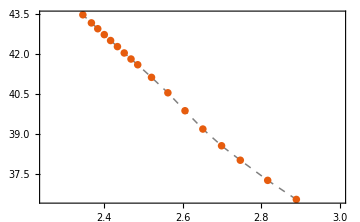

logNPplot.pdf

```mathematica
logNPplot=Show[ListLinePlot[logNP,
PlotTheme->"Scientific",
(*PlotMarkers->{omarker,.012},*)
PlotStyle->{Dashed,Thickness[.003],Gray},
PlotRange->{{2.25,3.},Automatic},
PlotRangePadding->{{0,0},{1,1}},
ImagePadding->{{48,48},{25,36}},
ImageSize->Medium,
GridLines->None],
ListPlot[logNP,
PlotStyle->{PointSize[.015],colors⟦1⟧}],
Epilog->Join[
(Inset[Evaluate@MaTeX[#1,
Magnification->.9],#2]&)@@@{
{"\\frac{\\SI{e3}{\\K}}{T}",Scaled[{1.08,0}]},
{"\\ln\\frac{np/T^3}{\\si{\\cm^{-6}.\\K^{-3}}}",Scaled[{0,1.12}]}
},
Inset[
Graphics[{EdgeForm[Dotted],Opacity[0],
Rectangle@@(Scaled/@#1)}],
Scaled[#2]]&@@@{
{{{0,0},{.36,.25}},{.435,1.2}}
}],
PlotRangeClipping->False]
Export@@{ToString[#]<>".pdf",ReleaseHold[#]}&@HoldForm@logNPplot
```

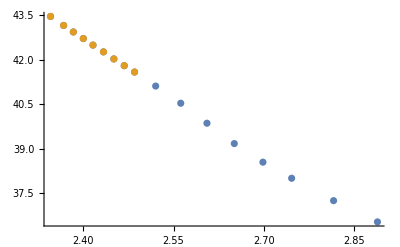

```mathematica
ListPlot[{logNP,logNP⟦-9;;⟧},PlotRange->All]
```

```mathematica
LinearModelFit[logNP⟦-9;;⟧,x,x]/@{"RSquared",x,"ParameterErrors"}//Column
```

0.999875
74.8349-13.3853 x
{0.136693,0.0565564}

```mathematica
kBsi=UnitSimplify[UnitConvert[Quantity["BoltzmannConstant"]]]
```

1.3806×10^-23 J/K

```mathematica
eVsi=UnitConvert[Quantity["Electronvolts"],"SI"]
```

1.602177×10^-19 J

```mathematica
QuantityMagnitude[kBsi]/QuantityMagnitude[eVsi]*(1.3)*10^4
```

1.12025